## Replicating the Figure 13

### Shared Helpers

```mathematica
(* ================================================================== *)
(* Figure 13 Replication: Suppress + Inject Position Sweep            *)
(* candle-mi example: figure13_planning_poems                         *)
(* ================================================================== *)

(* Shared helper: extract sweep data from a JSON association *)
extractSweep[d_] := Module[{sw = d["sweep"]},
  <|
    "positions" -> sw[[All, "position"]],
    "probs"     -> sw[[All, "prob"]],
    "tokens"    -> sw[[All, "token"]],
    "baseline"  -> d["baseline_prob"]
  |>]
```

```mathematica
(* Shared helper: clean token labels for display *)
cleanToken[t_] := StringReplace[t, {
  "\n" -> "\\n",
  " " -> " "}]
```

```mathematica
(* Shared helper: build styled bar data (first=dark gray, last=red, rest=gray) *)
styledBars[allProbs_, nAll_] := MapIndexed[
  Style[#1, Which[
    First[#2] == 1, GrayLevel[0.4],
    First[#2] == nAll, Darker[Red],
    True, GrayLevel[0.6]
  ]] &,
  allProbs]
```

### Llama 3.2 1B with 524K CLTs

```mathematica
(* Figure 13 Replication: Suppress + Inject Position Sweep *)
(* Llama 3.2 1B with 524K CLT *)
(* Import JSON output from candle-mi figure13_planning_poems example *)

llamaData = Import[
  FileNameJoin[{NotebookDirectory[], "llama_output.json"}],
  "RawJSON"
];

llamaSweep = extractSweep[llamaData];
llamaProbs = llamaSweep["probs"];
llamaTokens = llamaSweep["tokens"];
llamaBaseline = llamaSweep["baseline"];
llamaLabels = cleanToken /@ llamaTokens;

(* Prepend baseline as "No Steering" bar *)
llamaAllProbs = Prepend[llamaProbs, llamaBaseline];
llamaAllLabels = Prepend[llamaLabels, "No Steering"];
nLlama = Length[llamaAllProbs]
```

32

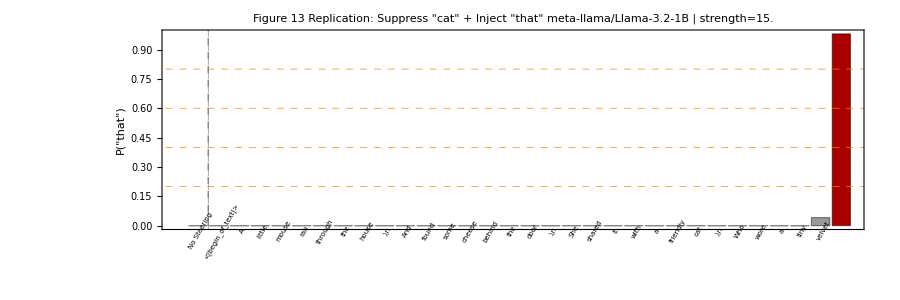

```mathematica
(* --- Bar chart (linear scale, full range) --- *)
fig13Linear =
Labeled[BarChart[styledBars[llamaAllProbs, nLlama],
ChartLabels->Placed[Style[#,7,FontFamily->"Consolas"]&/@allLabels,Below,Rotate[#,Pi/3]&],
PlotLabel -> Style["Figure 13 Replication: Suppress \"" <> data["suppress_word"] <> "\" + Inject \"" <> data["inject_word"] <> "\"\n" <> data["model"] <> " | strength=" <>  ToString[data["strength"]],12, Bold  ],
Frame -> True,FrameLabel -> {None,Style["P(\"" <> data["inject_word"] <> "\")", 11]},
GridLines->{{{1.5,Directive[Dashed,GrayLevel[0.5]]}},Table[gl,{gl,0.2,0.8,0.2}]},GridLinesStyle->Directive[Orange,Dashed],
ImageSize -> 900,AspectRatio -> 1/3,
PlotRangePadding -> {{Scaled[0.01], Scaled[0.01]}, {0, Scaled[0.05]}},
Epilog->{Dashed,Thin,GrayLevel[0.5],Line[{{1.5,0},{1.5,1}}]}],
Style["Token position",11],
Bottom]
```

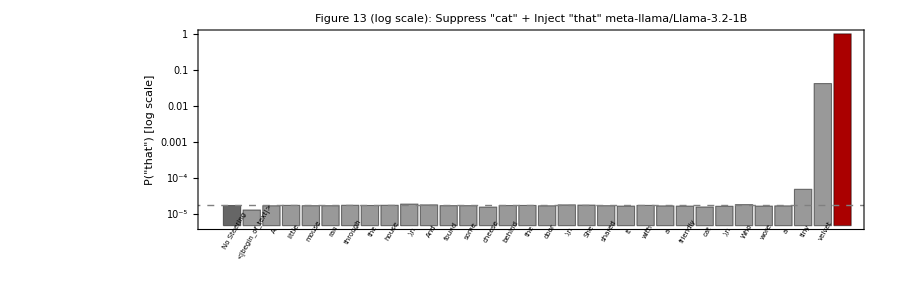

```mathematica
(* --- Bar chart (log scale) --- *)
fig13Log =
Labeled[ BarChart[styledBars[llamaAllProbs, nLlama],
ChartLabels->Placed[Style[#,7,FontFamily->"Consolas"]&/@allLabels,Below,Rotate[#,Pi/3]&],
ScalingFunctions -> "Log",
PlotLabel -> Style["Figure 13 (log scale): Suppress \"" <> data["suppress_word"] <> "\" + Inject \"" <> data["inject_word"] <>"\"\n" <> data["model"], 12, Bold ],
FrameLabel -> {None,Style["P(\"" <> data["inject_word"] <> "\") [log scale]", 11]},Frame -> True,
GridLines->{None,Table[10^-gl,{gl,0,5,1}]},GridLinesStyle->Directive[Orange,Dashed],
ImageSize -> 900,AspectRatio -> 1/3,
PlotRangePadding -> {{Scaled[0.01], Scaled[0.01]}, {0, Scaled[0.05]}},
Epilog -> {Dashed, Thin, GrayLevel[0.5],InfiniteLine[{0, Log[baseline]}, {1, 0}]}],
Style["Token position", 11],
Bottom]
```

#### Exporting the figures as PNG files

```mathematica
Export[
  FileNameJoin[{NotebookDirectory[], "figure13_linear.png"}],
  fig13Linear,
  ImageResolution -> 300
]
```

C:\Users\Eric JACOPIN\Documents\Code\Source\candle-mi\examples\figure13\figure13_linear.png

```mathematica
Export[
  FileNameJoin[{NotebookDirectory[], "figure13_log.png"}],
  fig13Log,
  ImageResolution -> 300
]
```

C:\Users\Eric JACOPIN\Documents\Code\Source\candle-mi\examples\figure13\figure13_log.png

### Gemma 2 2B with 426K CLTs

```mathematica
(* ================================================================== *)
(* PART 2: Gemma 2 2B                                                 *)
(* ================================================================== *)

gemmaData = Import[
  FileNameJoin[{NotebookDirectory[], "gemma_output.json"}],
  "RawJSON"
];

gemmaSweep = extractSweep[gemmaData];
gemmaProbs = gemmaSweep["probs"];
gemmaTokens = gemmaSweep["tokens"];
gemmaBaseline = gemmaSweep["baseline"];
gemmaLabels = cleanToken /@ gemmaTokens;

(* Prepend baseline as "No Steering" bar *)
gemmaAllProbs = Prepend[gemmaProbs, gemmaBaseline];
gemmaAllLabels = Prepend[gemmaLabels, "No Steering"];
nGemma = Length[gemmaAllProbs]
```

33

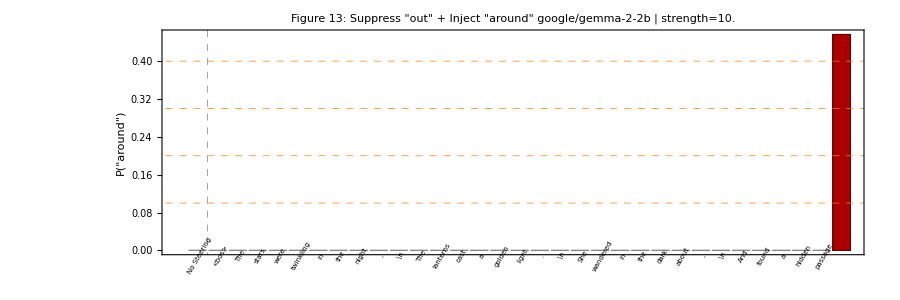

```mathematica
(* --- Gemma: linear scale --- *)
gemmaLinear =
Labeled[ BarChart[styledBars[gemmaAllProbs, nGemma],
ChartLabels -> Placed[Style[#,7, FontFamily -> "Consolas"] & /@ gemmaAllLabels,Below, Rotate[#, Pi/3] & ],PlotLabel -> Style["Figure 13: Suppress \"" <> gemmaData["suppress_word"] <> "\" + Inject \"" <> gemmaData["inject_word"] <> "\"\n" <> gemmaData["model"] <> " | strength=" <> ToString[gemmaData["strength"]],12, Bold ],Frame -> True,FrameLabel -> {None,Style["P(\"" <> gemmaData["inject_word"] <> "\")", 11]},
GridLines->{{{1.5,Directive[Dashed,GrayLevel[0.5]]}},Table[gl,{gl,0.1,0.8,0.1}]},GridLinesStyle->Directive[Orange,Dashed],
ImageSize -> 900,AspectRatio -> 1/3,PlotRangePadding -> {{Scaled[0.01], Scaled[0.01]}, {0, Scaled[0.05]}},
GridLines -> {{{1.5, Directive[Dashed, GrayLevel[0.5]]}}, None}],
Style["Token position", 11],
Bottom]
```

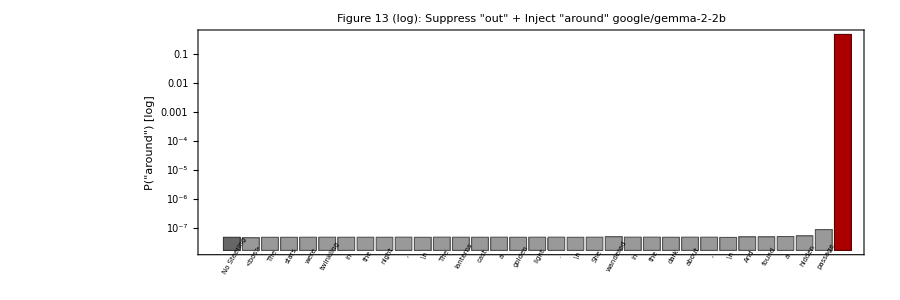

```mathematica
(* --- Gemma: log scale --- *)
gemmaLog = 
Labeled[BarChart[styledBars[gemmaAllProbs, nGemma],
ChartLabels -> Placed[Style[#, 7, FontFamily -> "Consolas"] & /@ gemmaAllLabels,Below, Rotate[#, Pi/3] &],
ScalingFunctions -> "Log",
PlotLabel -> Style["Figure 13 (log): Suppress \"" <> gemmaData["suppress_word"] <> "\" + Inject \"" <> gemmaData["inject_word"] <> "\"\n" <> gemmaData["model"],12, Bold ],
Frame -> True,FrameLabel -> {None,Style["P(\"" <> gemmaData["inject_word"] <> "\") [log]", 11]},
GridLines->{None,Table[10^-gl,{gl,0,7,1}]},GridLinesStyle->Directive[Orange,Dashed],
ImageSize -> 900,AspectRatio -> 1/3,
PlotRangePadding -> {{Scaled[0.01], Scaled[0.01]}, {0, Scaled[0.05]}},
GridLines -> {{{1.5, Directive[Dashed, GrayLevel[0.5]]}}, None}],
Style["Token position", 11],
Bottom]
```

#### Exporting the figures as PNG files

```mathematica
(* Export Gemma PNGs *)
Export[
  FileNameJoin[{NotebookDirectory[], "gemma_linear.png"}],
  gemmaLinear, ImageResolution -> 300
]
```

C:\Users\Eric JACOPIN\Documents\Code\Source\candle-mi\examples\figure13\gemma_linear.png

```mathematica
Export[
  FileNameJoin[{NotebookDirectory[], "gemma_log.png"}],
  gemmaLog, ImageResolution -> 300
]
```

C:\Users\Eric JACOPIN\Documents\Code\Source\candle-mi\examples\figure13\gemma_log.png

## Adding recurrent feedback

#### Loading the JSON files

```mathematica
(* ================================================================== *)
(* Recurrent Feedback (Anacrousis): Condition Comparison & Couplet          *)
(* Grid from JSON output.                                                   *)
(* candle-mi example: recurrent_feedback                                    *)
(*                                                                          *)
(* Usage:                                                                   *)
(*   1. Run the example with --output to produce JSON files:                *)
(*      cargo run --release --features transformer                          *)
(*        --example recurrent_feedback --                                   *)
(*        --output examples/results/recurrent_feedback/prefill.json         *)
(*      cargo run --release --features transformer                          *)
(*        --example recurrent_feedback -- --sustained                       *)
(*        --loop-start 14 --loop-end 15 --strength 1.0                      *)
(*        --output examples/results/recurrent_feedback/sustained.json       *)
(*   2. Open this .wl in Mathematica and evaluate.                          *)
(*                                                                          *)
(* References:                                                              *)
(*   Taufeeque et al., arXiv:2407.15421 (DRC planning in Sokoban)           *)
(*   Lindsey et al., "On the Biology of a Large Language Model", 2025       *)
(*   plip-rs anacrousis branch (28-condition experiment)                    *)
(* ================================================================== *)

(* ============================================================ *)
(* LOAD JSON DATA                                                    *)
(* ============================================================ *)

resultsDir = FileNameJoin[{
  NotebookDirectory[], "..", "results", "recurrent_feedback"
}];

prefillFile = FileNameJoin[{resultsDir, "prefill.json"}];
sustainedFile = FileNameJoin[{resultsDir, "sustained.json"}];

hasPrefill = FileExistsQ[prefillFile];
hasSustained = FileExistsQ[sustainedFile];

If[hasPrefill,
  prefillData = Import[prefillFile, "RawJSON"],
  Print["WARNING: " <> prefillFile <> " not found — run the example with --output"]
];
If[hasSustained,
  sustainedData = Import[sustainedFile, "RawJSON"],
  Print["WARNING: " <> sustainedFile <> " not found — run the example with --output"]
];
```

#### Shared Helpers: extract per-couplet data from a JSON association

```mathematica
(* Extract {id, target, baseline_word, baseline_ok, recurrent_word, recurrent_ok, result}
   from the "couplets" array in a JSON association. *)
extractCouplets[d_] := d["couplets"];

(* Build the grid and word arrays from one or two JSON runs.
   Each JSON has baseline + one recurrent condition.
   We merge them into a unified grid:
     col 1 = baseline (from prefill JSON — both share the same baseline)
     col 2 = prefill recurrent
     col 3 = sustained recurrent *)
```

#### Build Data Tables

```mathematica
If[hasPrefill && hasSustained,
  (* --- Both files available: 3-column grid --- *)
  pfCouplets = prefillData["couplets"];
  susCouplets = sustainedData["couplets"];
  nCouplets = Length[pfCouplets];

  modelId = prefillData["model_id"];
  nLayers = prefillData["n_layers"];

  coupletGrid = Table[
    {
      pfCouplets[[i, "id"]],
      pfCouplets[[i, "target"]],
      If[pfCouplets[[i, "baseline_rhymes"]], 1, 0],
      If[pfCouplets[[i, "recurrent_rhymes"]], 1, 0],
      If[susCouplets[[i, "recurrent_rhymes"]], 1, 0]
    },
    {i, nCouplets}
  ];

  generatedWords = Table[
    {
      pfCouplets[[i, "id"]],
      pfCouplets[[i, "baseline_word"]],
      pfCouplets[[i, "recurrent_word"]],
      susCouplets[[i, "recurrent_word"]]
    },
    {i, nCouplets}
  ];

  conditionLabels = {
    "Baseline",
    "Prefill\nL" <> ToString[prefillData["loop_start"]] <>
      "–" <> ToString[prefillData["loop_end"]] <>
      ", s=" <> ToString[prefillData["strength"]],
    "Sustained\nL" <> ToString[sustainedData["loop_start"]] <>
      "–" <> ToString[sustainedData["loop_end"]] <>
      ", s=" <> ToString[sustainedData["strength"]]
  };

  conditionRhymes = {
    prefillData["baseline_rhymes"],
    prefillData["recurrent_rhymes"],
    sustainedData["recurrent_rhymes"]
  };

  nCols = 3;
  baselineRhymes = prefillData["baseline_rhymes"],

  (* --- Only prefill available: 2-column grid --- *)
  If[hasPrefill && !hasSustained,
    pfCouplets = prefillData["couplets"];
    nCouplets = Length[pfCouplets];
    modelId = prefillData["model_id"];
    nLayers = prefillData["n_layers"];

    coupletGrid = Table[
      {
        pfCouplets[[i, "id"]],
        pfCouplets[[i, "target"]],
        If[pfCouplets[[i, "baseline_rhymes"]], 1, 0],
        If[pfCouplets[[i, "recurrent_rhymes"]], 1, 0]
      },
      {i, nCouplets}
    ];

    generatedWords = Table[
      {
        pfCouplets[[i, "id"]],
        pfCouplets[[i, "baseline_word"]],
        pfCouplets[[i, "recurrent_word"]]
      },
      {i, nCouplets}
    ];

    conditionLabels = {
      "Baseline",
      prefillData["mode"] <> "\nL" <>
        ToString[prefillData["loop_start"]] <>
        "–" <> ToString[prefillData["loop_end"]] <>
        ", s=" <> ToString[prefillData["strength"]]
    };

    conditionRhymes = {
      prefillData["baseline_rhymes"],
      prefillData["recurrent_rhymes"]
    };

    nCols = 2;
    baselineRhymes = prefillData["baseline_rhymes"],

    (* --- Neither file: abort --- *)
    Print["ERROR: No JSON files found. Run the example with --output first."];
    Abort[]
  ]
]
```

9

#### FIGURE 1: Condition Comparison Bar Chart

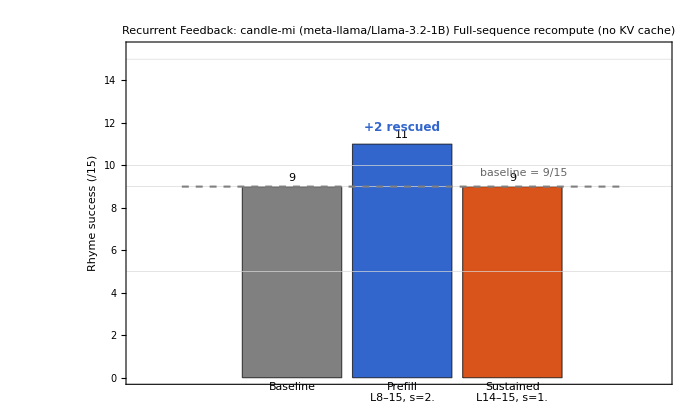

```mathematica
fig1 = Show[
  BarChart[conditionRhymes,
    ChartLabels -> Placed[
      Style[#, 11] & /@ conditionLabels,
      Below
    ],
    ChartStyle -> Take[
      {GrayLevel[0.5], RGBColor[0.2, 0.4, 0.8], RGBColor[0.85, 0.33, 0.1]},
      nCols
    ],
    Frame -> True,
    FrameLabel -> {
      None,
      Style["Rhyme success (/" <> ToString[nCouplets] <> ")", 14]
    },
    PlotLabel -> Style[
      "Recurrent Feedback: candle-mi (" <> modelId <> ")\n" <>
      "Full-sequence recompute (no KV cache)",
      16, Bold
    ],
    PlotRange -> {Automatic, {0, nCouplets + 0.5}},
    GridLines -> {None, {5, baselineRhymes, 10, nCouplets}},
    GridLinesStyle -> Directive[GrayLevel[0.85]],
    ImageSize -> 700,
    AspectRatio -> 0.6,
    ImagePadding -> {{60, 20}, {80, 50}},
    FrameTicks -> {{Range[0, nCouplets], Automatic}, {None, None}},
    LabelingFunction -> (Placed[#, Above] &)
  ],
  (* Baseline reference line *)
  Graphics[{
    Dashed, GrayLevel[0.5], AbsoluteThickness[1.5],
    Line[{{0, baselineRhymes}, {nCols + 1, baselineRhymes}}],
    Text[
      Style[
        "baseline = " <> ToString[baselineRhymes] <> "/" <> ToString[nCouplets],
        11, Italic, GrayLevel[0.4]
      ],
      {nCols + 0.5, baselineRhymes + 0.4}, {1, -1}
    ]
  }],
  (* Annotate rescued count on best condition *)
  If[Max[conditionRhymes] > baselineRhymes,
    Module[{bestIdx = First[Ordering[conditionRhymes, -1]], rescued},
      rescued = conditionRhymes[[bestIdx]] - baselineRhymes;
      Graphics[{
        RGBColor[0.2, 0.4, 0.8],
        Text[
          Style[
            "+" <> ToString[rescued] <> " rescued",
            12, Bold, RGBColor[0.2, 0.4, 0.8]
          ],
          {bestIdx, conditionRhymes[[bestIdx]] + 0.8}, {0, -1}
        ]
      }]
    ],
    Graphics[{}]
  ]
]
```

```mathematica
Export[
  FileNameJoin[{NotebookDirectory[], "recurrent_feedback_conditions.png"}],
  fig1, ImageResolution -> 300
];
```

```mathematica
(* ============================================================ *)
(* FIGURE 2: Per-Couplet Success Grid                            *)
(* ============================================================ *)

successColor = RGBColor[0.3, 0.75, 0.35];  (* Green *)
failureColor = RGBColor[0.9, 0.3, 0.3];    (* Red *)
convertColor = RGBColor[1.0, 0.85, 0.0];   (* Gold -- for conversion highlight *)

fig2grid = Table[
  Module[{val = coupletGrid[[row, col + 2]], word = generatedWords[[row, col + 1]]},
    {If[val == 1, successColor, failureColor],
     Rectangle[{col - 1, nCouplets - row}, {col, nCouplets + 1 - row}],
     Text[
       Style[word, 10, Bold, White],
       {col - 0.5, nCouplets + 0.5 - row}
     ]}
  ],
  {row, nCouplets}, {col, nCols}
]
```

```mathematica
(* Identify resistant failures: fail under ALL conditions *)
resistantIds = Select[
  Range[nCouplets],
  AllTrue[coupletGrid[[#, 3 ;; nCols + 2]], # == 0 &] &
]
```

{2,3,4,7}

```mathematica
resistantCoupletIds = coupletGrid[[#, 1]] & /@ resistantIds
```

{2,3,4,7}

```mathematica
(* Row labels: "1. light", "2. play", ... *)
rowLabels = Table[
  Text[
    Style[
      StringJoin[ToString[coupletGrid[[row, 1]]], ". ", coupletGrid[[row, 2]]],
      11,
      If[MemberQ[resistantIds, row], Bold, Plain],
      If[MemberQ[resistantIds, row], RGBColor[1.0, 0.4, 0.4], White]
    ],
    {-0.15, nCouplets + 0.5 - row}, {1, 0}
  ],
  {row, nCouplets}
]
```

{Text[1. light,{-0.15,14.5},{1,0}],Text[2. play,{-0.15,13.5},{1,0}],Text[3. sound,{-0.15,12.5},{1,0}],Text[4. rain,{-0.15,11.5},{1,0}],Text[5. time,{-0.15,10.5},{1,0}],Text[6. air,{-0.15,9.5},{1,0}],Text[7. gold,{-0.15,8.5},{1,0}],Text[8. fire,{-0.15,7.5},{1,0}],Text[9. stone,{-0.15,6.5},{1,0}],Text[10. dream,{-0.15,5.5},{1,0}],Text[11. strange,{-0.15,4.5},{1,0}],Text[12. love,{-0.15,3.5},{1,0}],Text[13. truth,{-0.15,2.5},{1,0}],Text[14. world,{-0.15,1.5},{1,0}],Text[15. earth,{-0.15,0.5},{1,0}]}

```mathematica
(* Column labels *)
colLabels = Table[
  Text[
    Style[conditionLabels[[col]], 10, Bold, White],
    {col - 0.5, nCouplets + 0.25}, {0, -1}
  ],
  {col, nCols}
]
```

{Text[Baseline,{0.5,15.25},{0,-1}],Text[Prefill
L8–15, s=2.,{1.5,15.25},{0,-1}],Text[Sustained
L14–15, s=1.,{2.5,15.25},{0,-1}]}

```mathematica
(* Find rescued couplets: baseline=0, any recurrent=1 *)
rescuedCells = {};
Do[
  Do[
    If[coupletGrid[[row, 3]] == 0 && coupletGrid[[row, col + 2]] == 1,
      AppendTo[rescuedCells, {row, col}]
    ],
    {col, 2, nCols}
  ],
  {row, nCouplets}
]
```

```mathematica
(* Gold border on rescued couplets *)
rescueHighlights = Table[
  {convertColor, AbsoluteThickness[3],
   Line[{
     {cell[[2]] - 1, nCouplets - cell[[1]]},
     {cell[[2]], nCouplets - cell[[1]]},
     {cell[[2]], nCouplets + 1 - cell[[1]]},
     {cell[[2]] - 1, nCouplets + 1 - cell[[1]]},
     {cell[[2]] - 1, nCouplets - cell[[1]]}
   }]},
  {cell, rescuedCells}
]
```

{{RGBColor[1., 0.85, 0.],AbsoluteThickness[3],Line[{{1,7},{2,7},{2,8},{1,8},{1,7}}]},{RGBColor[1., 0.85, 0.],AbsoluteThickness[3],Line[{{1,4},{2,4},{2,5},{1,5},{1,4}}]}}

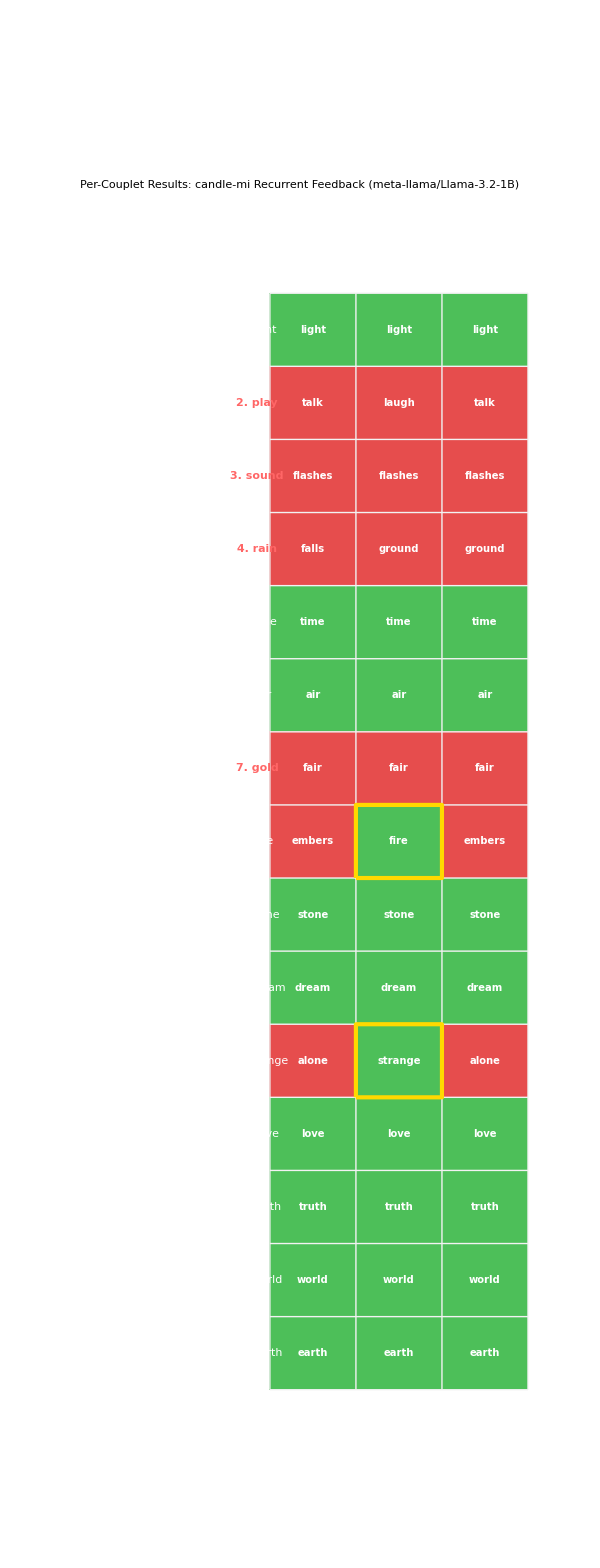

```mathematica
fig2 = Graphics[{
  (* Grid cells *)
  Flatten[fig2grid],
  (* Grid lines *)
  GrayLevel[0.95], AbsoluteThickness[1],
  Table[Line[{{0, y}, {nCols, y}}], {y, 0, nCouplets}],
  Table[Line[{{x, 0}, {x, nCouplets}}], {x, 0, nCols}],
  (* Labels *)
  rowLabels,
  colLabels,
  (* Conversion highlights *)
  rescueHighlights
  },
  PlotLabel -> Style[
    "Per-Couplet Results: candle-mi Recurrent Feedback (" <> modelId <> ")",
    14, Bold
  ],
  ImageSize -> 600,
  PlotRange -> {{-2.5, nCols + 0.2}, {-0.5, nCouplets + 1}},
  PlotRangePadding -> {{0, 0.2}, {0.3, 0.5}}
]
```

```mathematica
Export[
  FileNameJoin[{NotebookDirectory[], "recurrent_feedback_couplet_grid.png"}],
  fig2, ImageResolution -> 300]
```

```mathematica
(* ============================================================ *)
(* Summary                                                       *)
(* ============================================================ *)

Print["\n=== Summary ==="];
Print["Model:          ", modelId];
Print["Conditions:     ", nCols];
Print["Couplets:       ", nCouplets];
Print["Baseline:       ", baselineRhymes, "/", nCouplets];
Print["Best recurrent: ", Max[conditionRhymes], "/", nCouplets];
If[Length[rescuedCells] > 0,
  Print["Rescued cells:  ", Length[rescuedCells]],
  Print["Rescued cells:  0"]
];
If[Length[resistantCoupletIds] > 0,
  Print["Resistant failures: ", resistantCoupletIds]
];
```

=== Summary ===

Model:          meta-llama/Llama-3.2-1B

Conditions:     3

Couplets:       15

Baseline:       9/15

Best recurrent: 11/15

Rescued cells:  2

Resistant failures: {2,3,4,7}